## Using EpidemicKabu to estimate the size of the COVID-19 epidemic waves

The estimations of the waves and measures of the waves size were made with the epidemic curve of an indicator of incident cases instead of just  the data of incident cases. The indicator the ratio between the cases of each date and the total population size by year multiplied per 100. We assume that the total population size of each country represent the susceptible population.

## Initialization

### Getting the data

```mathematica
data=Import["/Users/linaruiz/Documents/EpidemicKabu_project/EpidemicKabuLibrary/examples/data/wavesSizes.csv"];
Length@data
data[[;;10]]//Grid
data[[2;;,1]]//Union
data[[2;;,1]]//Union//Length
```

92

Country | waveNum | max | sum | spanDays | ratioSumSpan
Belgium | 0 | 0.0107959 | 0.527542 | 170 | 0.00310319
Belgium | 1 | 0.0997438 | 5.15165 | 199 | 0.0258877
Belgium | 2 | 0.035368 | 3.62333 | 169 | 0.0214398
Belgium | 3 | 0.132126 | 7.41145 | 173 | 0.0428407
Belgium | 4 | 0.316606 | 14.644 | 87 | 0.168322
Belgium | 5 | 0.0855082 | 4.3808 | 81 | 0.054084
Belgium | 6 | 0.0523065 | 2.93466 | 99 | 0.029643
Belgium | 7 | 0.0153611 | 0.316462 | 21 | 0.0150696
Bosnia and Herzegovina | 0 | 0.0011689 | 0.0534485 | 123 | 0.000434541

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

15

### Ordering the data

```mathematica
data2=Table[MapAt[{i,#}&,GroupBy[data[[2;;]],First][[i]],{All,3;;}],{i,1,15}];
data2[[;;2]]
```

{{{Belgium,0,{1,0.0107959},{1,0.527542},{1,170},{1,0.00310319}},{Belgium,1,{1,0.0997438},{1,5.15165},{1,199},{1,0.0258877}},{Belgium,2,{1,0.035368},{1,3.62333},{1,169},{1,0.0214398}},{Belgium,3,{1,0.132126},{1,7.41145},{1,173},{1,0.0428407}},{Belgium,4,{1,0.316606},{1,14.644},{1,87},{1,0.168322}},{Belgium,5,{1,0.0855082},{1,4.3808},{1,81},{1,0.054084}},{Belgium,6,{1,0.0523065},{1,2.93466},{1,99},{1,0.029643}},{Belgium,7,{1,0.0153611},{1,0.316462},{1,21},{1,0.0150696}}},{{Bosnia and Herzegovina,0,{2,0.0011689},{2,0.0534485},{2,123},{2,0.000434541}},{Bosnia and Herzegovina,1,{2,0.0365759},{2,3.55836},{2,266},{2,0.0133773}},{Bosnia and Herzegovina,2,{2,0.0370349},{2,2.60634},{2,157},{2,0.0166009}},{Bosnia and Herzegovina,3,{2,0.0209914},{2,1.89189},{2,141},{2,0.0134176}},{Bosnia and Herzegovina,4,{2,0.0494252},{2,3.41782},{2,184},{2,0.0185751}},{Bosnia and Herzegovina,5,{2,0.00978714},{2,0.650881},{2,128},{2,0.005085}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Croatia"]&]
```

{{{Croatia,0,{5,0.00143939},{5,0.0547028},{5,148},{5,0.000369614}},{Croatia,1,{5,0.00614144},{5,0.276461},{5,109},{5,0.00253634}},{Croatia,2,{5,0.080625},{5,5.4654},{5,152},{5,0.0359566}},{Croatia,3,{5,0.05012},{5,3.02184},{5,137},{5,0.0220572}},{Croatia,4,{5,0.118223},{5,7.35489},{5,167},{5,0.0440412}},{Croatia,5,{5,0.195785},{5,11.8733},{5,171},{5,0.0694344}},{Croatia,6,{5,0.0315822},{5,2.27655},{5,115},{5,0.0197961}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Italy"]&]
```

{{{Italy,0,{7,0.00652017},{7,0.405651},{7,185},{7,0.00219271}},{Italy,1,{7,0.0460495},{7,3.76802},{7,206},{7,0.0182913}},{Italy,2,{7,0.0333955},{7,2.9953},{7,150},{7,0.0199687}},{Italy,3,{7,0.00985211},{7,0.705376},{7,99},{7,0.00712501}},{Italy,4,{7,0.227824},{7,21.3037},{7,235},{7,0.090654}},{Italy,5,{7,0.122829},{7,8.57459},{7,124},{7,0.0691499}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Luxem"]&]
```

{{{Luxembourg,0,{8,0.0111665},{8,0.504484},{8,145},{8,0.0034792}},{Luxembourg,1,{8,0.00937485},{8,0.453211},{8,82},{8,0.00552697}},{Luxembourg,2,{8,0.086608},{8,7.10284},{8,170},{8,0.0417814}},{Luxembourg,3,{8,0.0319201},{8,3.05956},{8,133},{8,0.0230042}},{Luxembourg,4,{8,0.0131414},{8,0.66708},{8,61},{8,0.0109357}},{Luxembourg,5,{8,0.248864},{8,26.635},{8,283},{8,0.0941166}},{Luxembourg,6,{8,0.099833},{8,6.49364},{8,114},{8,0.0569617}},{Luxembourg,7,{8,0.0218511},{8,0.232519},{8,11},{8,0.0211381}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Norw"]&]
```

{{{Norway,0,{9,0.00201503},{9,0.164671},{9,174},{9,0.000946385}},{Norway,1,{9,0.0115255},{9,2.21516},{9,359},{9,0.00617035}},{Norway,2,{9,0.234575},{9,24.5763},{9,466},{9,0.0527389}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Rep"]&]
```

{{{Republic of Korea,0,{10,0.000333231},{10,0.0223858},{10,143},{10,0.000156544}},{Republic of Korea,1,{10,0.00136445},{10,0.151262},{10,280},{10,0.000540223}},{Republic of Korea,2,{10,0.454465},{10,35.0655},{10,472},{10,0.0742914}},{Republic of Korea,3,{10,0.170172},{10,12.6344},{10,104},{10,0.121485}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Kin"]&]
```

{{{The United Kingdom,0,{13,0.00641652},{13,0.433809},{13,192},{13,0.00225942}},{The United Kingdom,1,{13,0.067364},{13,6.2619},{13,292},{13,0.0214449}},{The United Kingdom,2,{13,0.0503817},{13,2.39076},{13,97},{13,0.0246471}},{The United Kingdom,3,{13,0.211633},{13,19.1729},{13,207},{13,0.0926226}},{The United Kingdom,4,{13,0.100733},{13,4.7894},{13,85},{13,0.0563458}},{The United Kingdom,5,{13,0.0316702},{13,2.02752},{13,126},{13,0.0160915}}}}

## Plots of paper Version 1

### Plot1 - ListPlot

For all the waves of each country  is made a ListPlot of the “Total number of cases/totalPop*100”,  “Maximum number of cases/totalPop*100”, “Wave span in days” (Duration), and “Ratio sum/span by waves”

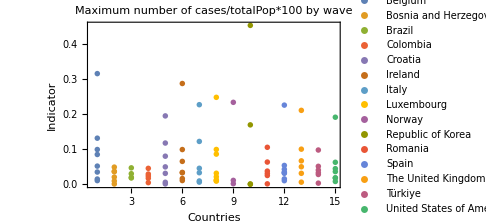
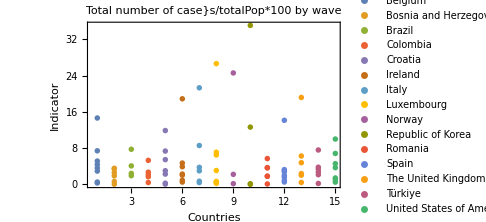
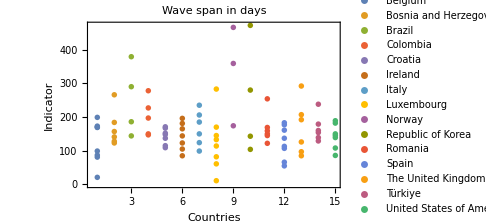
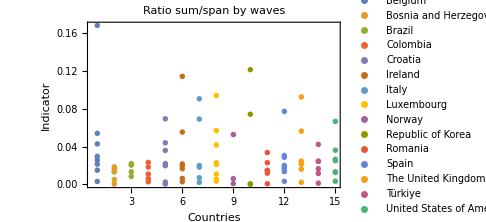

```mathematica
listPlot=ListPlot[#[[1]],PlotLabel->#[[2]],PlotRange->All,ImageSize->Medium,Frame->True,FrameLabel->{"Countries","Indicator"},PlotLegends->data2[[All,1,1]]]&/@{
{data2[[All,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data2[[All,All,4]],"Total number of case}s/totalPop*100 by wave"},
{data2[[All,All,5]],"Wave span in days"},
{data2[[All,All,6]],"Ratio sum/span by waves"}}
```

```mathematica
listPlot2=ListPlot[#[[1]],PlotLabel->#[[2]],PlotRange->All,ImageSize->Medium,Frame->True,FrameLabel->{"Countries","Indicator"},PlotStyle->Black]&/@{{data2[[All,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data2[[All,All,4]],"Total number of cases/totalPop*100 by wave"},
{data2[[All,All,5]],"Wave span in days"},
{data2[[All,All,6]],"Ratio sum/span by waves"}};
(*This listPlot2 is the same as listPlot2 but without Legends*)
```

### Plot2 - BoxPlot

For all the waves of each country  is made a BoxWhiskerChart of the “Total number of cases/totalPop*100”,  “Maximum number of cases/totalPop*100”, “Wave span in days” (Duration), and “Ratio sum/span by waves”

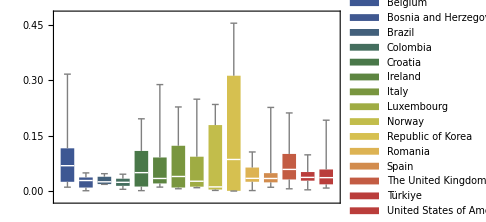
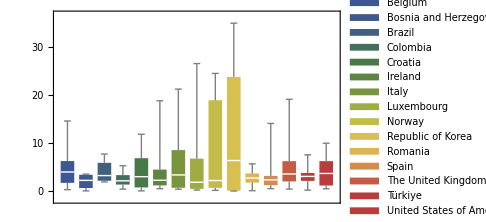
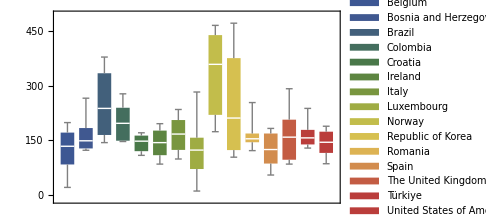
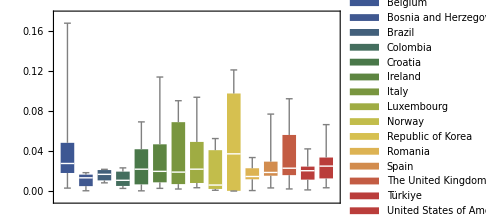

```mathematica
data3=GroupBy[data,First];
boxPlot=BoxWhiskerChart[#[[1]],(*ChartLabels->Echo[#[[2]]],*)ChartLegends->(data3[[2;;,1]]//Keys), ChartStyle->"DarkRainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black,12]]&/@{
{data3[[2;;,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data3[[2;;,All,4]],"Total number of cases/totalPop*100 by wave"},
{data3[[2;;,All,5]],"Wave span in days"},
{data3[[2;;,All,6]],"Ratio sum/span by waves"}}
```

```mathematica
(*VERSION WITH LABELS IN THE X-AXIS*)
(*labels=Rotate[#,Pi/2]&/@(data3[[2;;,1]]//Keys)
data3=GroupBy[data,First];
boxPlot=BoxWhiskerChart[#[[1]],ChartLabels->labels,ChartStyle->"DarkRainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black,12]]&/@{
{data3[[2;;,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data3[[2;;,All,4]],"Total number of cases/totalPop*100 by wave"},
{data3[[2;;,All,5]],"Wave span in days"},
{data3[[2;;,All,6]],"Ratio sum/span by waves"}}*)
```

### Plot 3 - Merging

Merging the ListPlot and BoxWhiskerChart

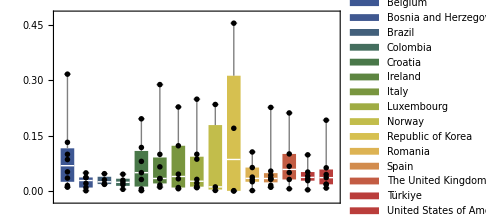
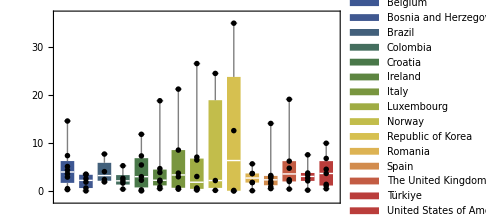
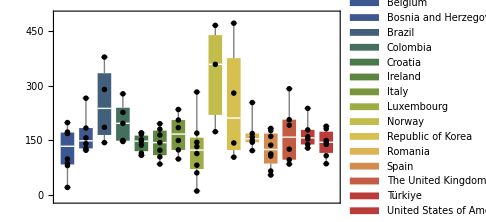
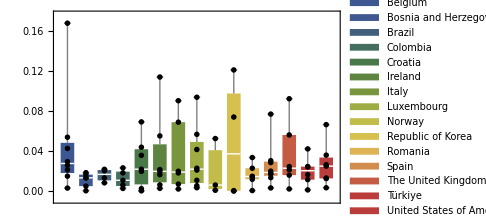

```mathematica
Show[boxPlot[[#]],listPlot2[[#]]]&/@{1,2,3,4}
```

### Plot 4 - All data in a boxplot

Plotting the Total number of cases/totalPop*100”|”Maximum number of cases/totalPop*100”|”Maximum number of cases/totalPop*100 normalized”  values of for all the waves of all countries in a unique BoxWhiskerChart and repeating this plot as many countries there are

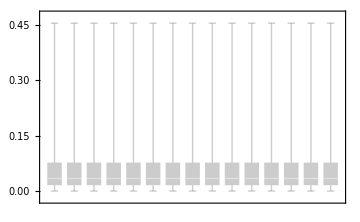
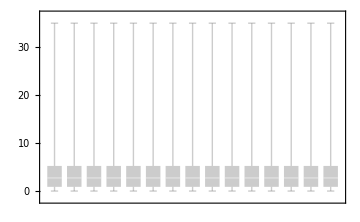
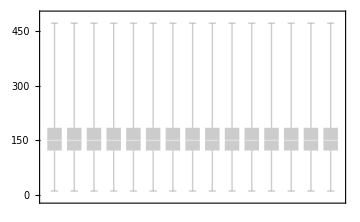
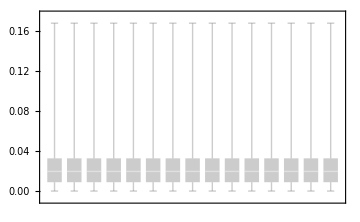

```mathematica
allBoxPlot=BoxWhiskerChart[Table[Flatten@GatherBy[data[[2;;]],First][[All,All,#[[1]]]],Length[data2[[All,1,1]]]],ImageSize->Medium,ChartStyle->Opacity[0.4,Gray],FrameTicksStyle->Directive[Black,12]]&/@{
{3,"Maximum number of cases/totalPop*100 by wave"},
{4,"Total number of cases/totalPop*100 by wave"},
{5,"Wave span in days"},
{6,"Ratio sum/span by waves"}}
```

### Plot 5 - Merging

Plotting the Total number of cases/totalPop*100”|”Maximum number of cases/totalPop*100”|”Maximum number of cases/totalPop*100 normalized”  values of for all the waves of all countries in a unique BoxWhiskerChart and repeating this plot as many countries there are, and adding the points of the values belonging to each country

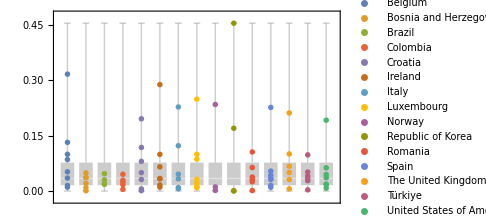
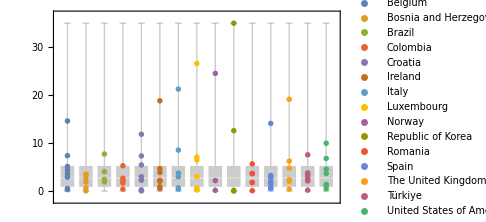
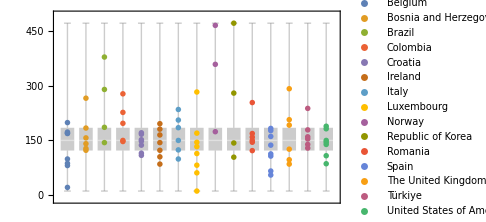
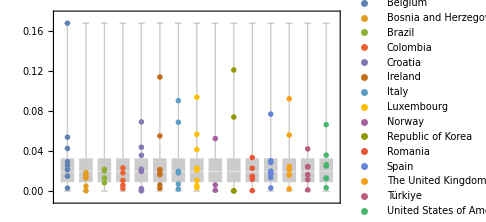

```mathematica
Show[allBoxPlot[[#]],listPlot[[#]]]&/@{1,2,3,4}
```

## Summary

This is used to write about this plot in the paper

### Summary of the estimations for each country

```mathematica
countries=data[[2;;,1]]//DeleteDuplicates
```

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

#### Maximum value

Getting some basic descriptions

```mathematica
descriptions={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Normal[GroupBy[data[[2;;]],First][[All,All,3]]]
```

{{Belgium,0.0107959,0.316606,0.093477,0.0995656,0.00991331},{Bosnia and Herzegovina,0.0011689,0.0494252,0.0258306,0.0183669,0.000337343},{Brazil,0.0184182,0.0473232,0.0290863,0.0133123,0.000177219},{Colombia,0.00505022,0.045901,0.0244028,0.0150973,0.000227929},{Croatia,0.00143939,0.195785,0.0691308,0.0694076,0.00481742},{Ireland,0.0109901,0.288356,0.0784557,0.0974699,0.00950037},{Italy,0.00652017,0.227824,0.0744118,0.08619,0.00742871},{Luxembourg,0.00937485,0.248864,0.0653449,0.0820478,0.00673184},{Norway,0.00201503,0.234575,0.0827053,0.131609,0.017321},{Republic of Korea,0.000333231,0.454465,0.156584,0.214029,0.0458083},{Romania,0.00162888,0.106047,0.0443865,0.0362819,0.00131637},{Spain,0.0105523,0.226597,0.0563663,0.0701764,0.00492473},{The United Kingdom,0.00641652,0.211633,0.0780331,0.0728301,0.00530422},{Türkiye,0.00361621,0.0982748,0.0427418,0.031593,0.000998118},{United States of America,0.00843926,0.192028,0.0546319,0.0633809,0.00401714}}

```mathematica
countriesOrderedByMaximum=Reverse@SortBy[descriptions,#[[4]]&]
```

{{Republic of Korea,0.000333231,0.454465,0.156584,0.214029,0.0458083},{Belgium,0.0107959,0.316606,0.093477,0.0995656,0.00991331},{Norway,0.00201503,0.234575,0.0827053,0.131609,0.017321},{Ireland,0.0109901,0.288356,0.0784557,0.0974699,0.00950037},{The United Kingdom,0.00641652,0.211633,0.0780331,0.0728301,0.00530422},{Italy,0.00652017,0.227824,0.0744118,0.08619,0.00742871},{Croatia,0.00143939,0.195785,0.0691308,0.0694076,0.00481742},{Luxembourg,0.00937485,0.248864,0.0653449,0.0820478,0.00673184},{Spain,0.0105523,0.226597,0.0563663,0.0701764,0.00492473},{United States of America,0.00843926,0.192028,0.0546319,0.0633809,0.00401714},{Romania,0.00162888,0.106047,0.0443865,0.0362819,0.00131637},{Türkiye,0.00361621,0.0982748,0.0427418,0.031593,0.000998118},{Brazil,0.0184182,0.0473232,0.0290863,0.0133123,0.000177219},{Bosnia and Herzegovina,0.0011689,0.0494252,0.0258306,0.0183669,0.000337343},{Colombia,0.00505022,0.045901,0.0244028,0.0150973,0.000227929}}

Countries with the lowest Maximum value by wave

```mathematica
Select[descriptions,#[[2]]==Min[descriptions[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.000333231}}

Countries with the highest Maximum value by wave

```mathematica
Select[descriptions,#[[3]]==Max[descriptions[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,0.454465}}

Countries with the lowest mean of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[4]]==Min[descriptions[[All,4]]]&][[All,{1,4}]]
```

{{Colombia,0.0244028}}

Countries with the highest mean of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[4]]==Max[descriptions[[All,4]]]&][[All,{1,4}]]
```

{{Republic of Korea,0.156584}}

Countries with the lowest sd of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[5]]==Min[descriptions[[All,5]]]&][[All,{1,5}]]
```

{{Brazil,0.0133123}}

Countries with the highest sd of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[5]]==Max[descriptions[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,0.214029}}

Countries with the lowest variance of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[6]]==Min[descriptions[[All,6]]]&][[All,{1,6}]]
```

{{Brazil,0.000177219}}

Countries with the highest variance of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[6]]==Max[descriptions[[All,6]]]&][[All,{1,6}]]
```

{{Republic of Korea,0.0458083}}

#### Total

Getting some basic descriptions

```mathematica
descriptionsT={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,4]]];
```

```mathematica
countriesOrderedByTotal=Reverse@SortBy[descriptionsT,#[[4]]&]
```

{{Republic of Korea,0.0223858,35.0655,11.9684,16.4952,272.091},{Norway,0.164671,24.5763,8.98538,13.541,183.359},{Italy,0.405651,21.3037,6.2921,7.92034,62.7319},{The United Kingdom,0.433809,19.1729,5.84604,6.85137,46.9412},{Luxembourg,0.232519,26.635,5.64354,8.9248,79.6521},{Belgium,0.316462,14.644,4.87374,4.5857,21.0287},{Ireland,0.51513,18.873,4.74583,6.40721,41.0524},{Croatia,0.0547028,11.8733,4.33187,4.2422,17.9962},{Brazil,1.91942,7.7481,4.0431,2.63636,6.95041},{United States of America,0.497325,10.0044,4.01543,3.46055,11.9754},{Spain,0.527586,14.1359,3.52707,4.40043,19.3638},{Türkiye,0.206504,7.58733,3.31335,2.44277,5.96712},{Romania,0.093303,5.69812,2.79104,1.96144,3.84726},{Colombia,0.417531,5.30303,2.45356,1.80205,3.24737},{Bosnia and Herzegovina,0.0534485,3.55836,2.02979,1.44374,2.08438}}

Countries with the lowest Total by wave

```mathematica
Select[descriptionsT,#[[2]]==Min[descriptionsT[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.0223858}}

Countries with the highest Total by wave

```mathematica
Select[descriptionsT,#[[3]]==Max[descriptionsT[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,35.0655}}

Countries with the lowest mean of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[4]]==Min[descriptionsT[[All,4]]]&][[All,{1,4}]]
```

{{Bosnia and Herzegovina,2.02979}}

Countries with the highest mean of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[4]]==Max[descriptionsT[[All,4]]]&][[All,{1,4}]]
```

{{Republic of Korea,11.9684}}

Countries with the lowest sd of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[5]]==Min[descriptionsT[[All,5]]]&][[All,{1,5}]]
```

{{Bosnia and Herzegovina,1.44374}}

Countries with the highest sd of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[5]]==Max[descriptionsT[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,16.4952}}

Countries with the lowest variance of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[6]]==Min[descriptionsT[[All,6]]]&][[All,{1,6}]]
```

{{Bosnia and Herzegovina,2.08438}}

Countries with the highest variance of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[6]]==Max[descriptionsT[[All,6]]]&][[All,{1,6}]]
```

{{Republic of Korea,272.091}}

#### Duration in days

Getting some basic descriptions

```mathematica
descriptionsD={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,5]]];
```

```mathematica
countriesOrderedByDuration=Reverse@SortBy[descriptionsD,#[[4]]&]
```

{{Norway,174,466,333,√21823,21823},{Republic of Korea,104,472,999/4,(√(331795/3))/2,331795/12},{Brazil,144,379,999/4,(√(134291/3))/2,134291/12},{Colombia,147,278,999/5,√(30327/10),30327/10},{Türkiye,129,238,333/2,√(15259/10),15259/10},{The United Kingdom,85,292,333/2,3 √(6923/10),62307/10},{Romania,122,254,333/2,√(20867/10),20867/10},{Italy,99,235,333/2,√(26459/10),26459/10},{Bosnia and Herzegovina,123,266,333/2,√(28643/10),28643/10},{United States of America,86,189,999/7,2 √(7157/21),28628/21},{Ireland,85,196,999/7,√(11603/7),11603/7},{Croatia,109,171,999/7,√(4015/7),4015/7},{Spain,55,183,999/8,(√(130855/14))/2,130855/56},{Luxembourg,11,283,999/8,(√(372119/14))/2,372119/56},{Belgium,21,199,999/8,(√(212903/14))/2,212903/56}}

Countries with the lowest Duration in days by wave

```mathematica
Select[descriptionsD,#[[2]]==Min[descriptionsD[[All,2]]]&][[All,{1,2}]]
```

{{Luxembourg,11}}

Countries with the highest Duration in days by wave

```mathematica
Select[descriptionsD,#[[3]]==Max[descriptionsD[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,472}}

Countries with the lowest mean of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[4]]==Min[descriptionsD[[All,4]]]&][[All,{1,4}]]
```

{{Belgium,124.875},{Luxembourg,124.875},{Spain,124.875}}

Countries with the highest mean of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[4]]==Max[descriptionsD[[All,4]]]&][[All,{1,4}]]
```

{{Norway,333.}}

Countries with the lowest sd of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[5]]==Min[descriptionsD[[All,5]]]&][[All,{1,5}]]
```

{{The United Kingdom,36.8799}}

Countries with the highest sd of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[5]]==Max[descriptionsD[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,166.282}}

#### Ratio

Getting some basic descriptions

```mathematica
descriptionsR={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,6]]];
```

```mathematica
countriesOrderedByRatio=Reverse@SortBy[descriptionsR,#[[4]]&]
```

{{Republic of Korea,0.000156544,0.121485,0.0491183,0.0595194,0.00354256},{Belgium,0.00310319,0.168322,0.0450488,0.0522397,0.00272899},{The United Kingdom,0.00225942,0.0926226,0.0355685,0.0331496,0.00109889},{Italy,0.00219271,0.090654,0.0345636,0.0363893,0.00132418},{Ireland,0.00284602,0.114382,0.0338705,0.0393887,0.00155147},{Luxembourg,0.0034792,0.0941166,0.032118,0.0310161,0.000961999},{Croatia,0.000369614,0.0694344,0.0277416,0.0243291,0.000591904},{United States of America,0.00342983,0.0666959,0.0262562,0.0208598,0.000435131},{Spain,0.00327693,0.0772455,0.0260384,0.0223793,0.000500835},{Türkiye,0.00129065,0.0423873,0.0201518,0.0139586,0.000194842},{Norway,0.000946385,0.0527389,0.0199519,0.0285143,0.000813063},{Romania,0.000643469,0.0337167,0.0164533,0.011111,0.000123454},{Brazil,0.00836771,0.021926,0.0160166,0.00633102,0.0000400819},{Colombia,0.00278354,0.0233614,0.0123061,0.0085135,0.0000724797},{Bosnia and Herzegovina,0.000434541,0.0185751,0.0112484,0.00702131,0.0000492989}}

Countries with the lowest Ratio by wave

```mathematica
Select[descriptionsR,#[[2]]==Min[descriptionsR[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.000156544}}

Countries with the highest Ratio  by wave

```mathematica
Select[descriptionsR,#[[3]]==Max[descriptionsR[[All,3]]]&][[All,{1,3}]]
```

{{Belgium,0.168322}}

Countries with the lowest mean of  the ratio  of their set of waves

```mathematica
Select[descriptionsR,#[[4]]==Min[descriptionsR[[All,4]]]&][[All,{1,4}]]
```

{{Bosnia and Herzegovina,0.0112484}}

Countries with the highest mean of  the ratios  of their set of waves

```mathematica
Select[descriptionsR,#[[4]]==Max[descriptionsR[[All,4]]]&][[All,{1,4}]]
```

{{Republic of Korea,0.0491183}}

Countries with the lowest sd of  the ratios of their set of waves

```mathematica
Select[descriptionsR,#[[5]]==Min[descriptionsR[[All,5]]]&][[All,{1,5}]]
```

{{Brazil,0.00633102}}

Countries with the highest sd of  the ratios of their set of waves

```mathematica
Select[descriptionsR,#[[5]]==Max[descriptionsR[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,0.0595194}}

### Summary of the estimations for all the countries at once

```mathematica
countries=data[[2;;,1]]//DeleteDuplicates
```

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

#### Maximum value

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,3]]
```

{0.000333231,0.454465,0.0642007,0.0806066}

#### Total

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,4]]
```

{0.0223858,35.0655,4.7133,6.24178}

#### Duration in days

Getting some basic descriptions

```mathematica
descriptions=N@{
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,5]]
```

{11.,472.,164.67,78.7}

#### Ratio

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,6]]
```

{0.000156544,0.168322,0.0278083,0.0300781}

## Plots of paper Version 2

### Ordered by the mean value

### Plot 1

Merging the ListPlot and BoxWhiskerChart

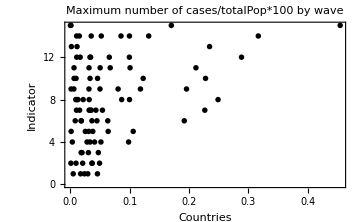
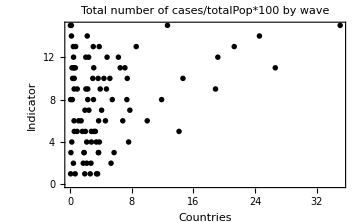
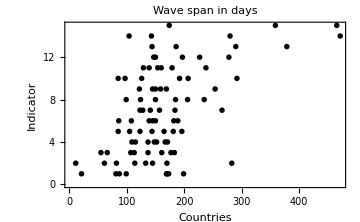
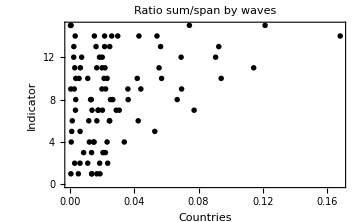

```mathematica
listPlot2=ListPlot[
(*Echo@*)Table[{#,i}&/@(#[[2]]/.#[[1]])[[i]],{i,1,15}],
PlotLabel->#[[3]],
PlotRange->All,
ImageSize->Medium,
Frame->True,
FrameLabel->{"Countries","Indicator"},
PlotStyle->Black
]&/@{
{Thread[data2[[All,All,1]][[All,1]]->data2[[All,All,3,2]]],Reverse@countriesOrderedByMaximum[[All,1]],"Maximum number of cases/totalPop*100 by wave"},
{Thread[data2[[All,All,1]][[All,1]]->data2[[All,All,4,2]]],Reverse@countriesOrderedByTotal[[All,1]],"Total number of cases/totalPop*100 by wave"},
{Thread[data2[[All,All,1]][[All,1]]->data2[[All,All,5,2]]],Reverse@countriesOrderedByDuration[[All,1]],
"Wave span in days"},
{Thread[data2[[All,All,1]][[All,1]]->data2[[All,All,6,2]]],Reverse@countriesOrderedByRatio[[All,1]],
"Ratio sum/span by waves"}
}
(*This listPlot2 is the same as listPlot2 but without Legends*)
```

### Plot 2

For all the waves of each country  is made a BoxWhiskerChart of the “Total number of cases/totalPop*100”,  “Maximum number of cases/totalPop*100”, “Maximum number of cases/totalPop*100 normalized”

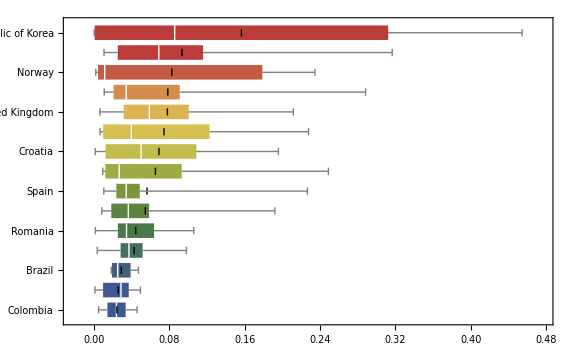
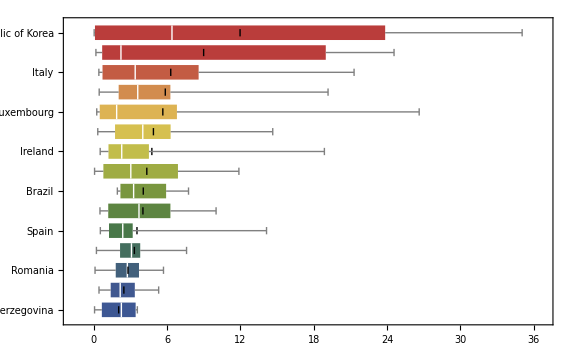
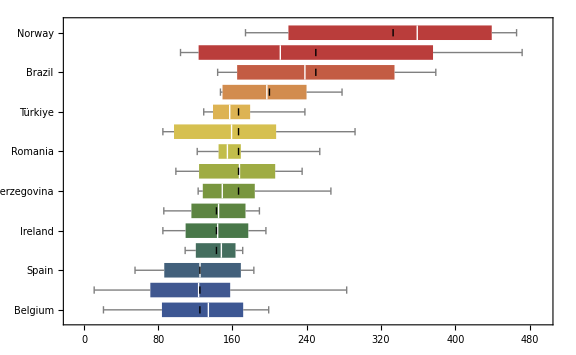
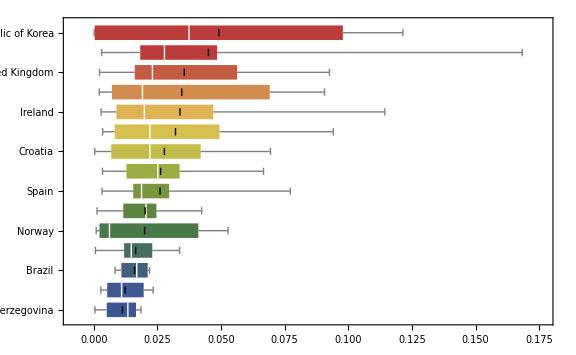

```mathematica
data3v2=GroupBy[data,First];
boxPlot=BoxWhiskerChart[
#[[2]]/.Normal[#[[1]]],
"Mean",
BarOrigin->Left,
ChartLabels->#[[2]],
ChartStyle->"DarkRainbow",
ImageSize->Large,
FrameTicksStyle->Directive[Black,12]
]&/@{
{data3[[2;;,All,3]],Reverse@countriesOrderedByMaximum[[All,1]],"Maximum number of cases/totalPop*100 by wave"},
{data3[[2;;,All,4]],Reverse@countriesOrderedByTotal[[All,1]],"Total number of cases/totalPop*100 by wave"},
{data3[[2;;,All,5]],Reverse@countriesOrderedByDuration[[All,1]],"Wave span in days"},
{data3[[2;;,All,6]],Reverse@countriesOrderedByRatio[[All,1]],"Ratio sum/span by waves"}}
```

### Plot 3

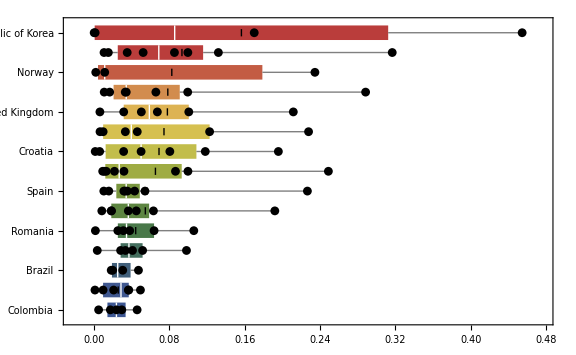
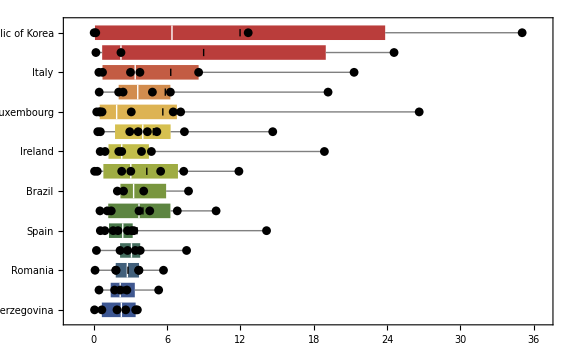
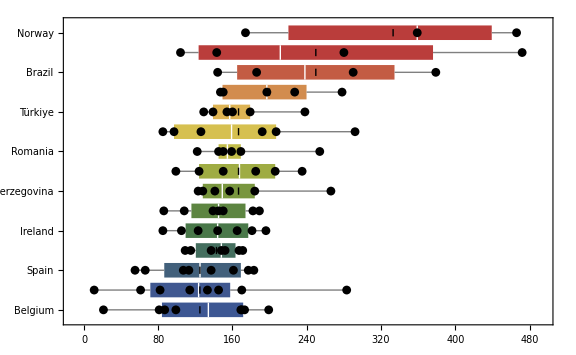
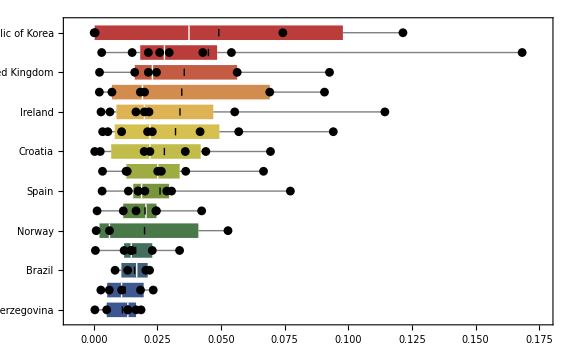

```mathematica
Show[boxPlot[[#]],listPlot2[[#]]]&/@{1,2,3,4}
```

### Plot 4 - All data in a boxplot

Plotting the Total number of cases/totalPop*100”|”Maximum number of cases/totalPop*100”|”Maximum number of cases/totalPop*100 normalized”  values of for all the waves of all countries in a unique BoxWhiskerChart and repeating this plot as many countries there are

```mathematica
{,,,}
```

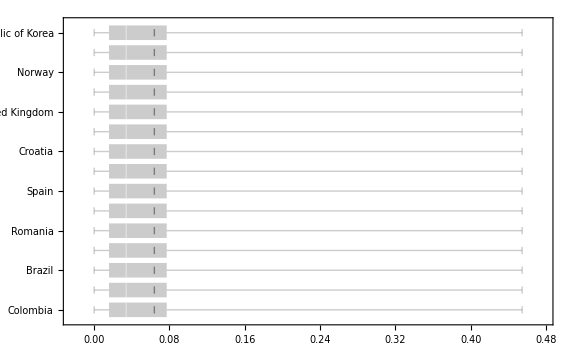
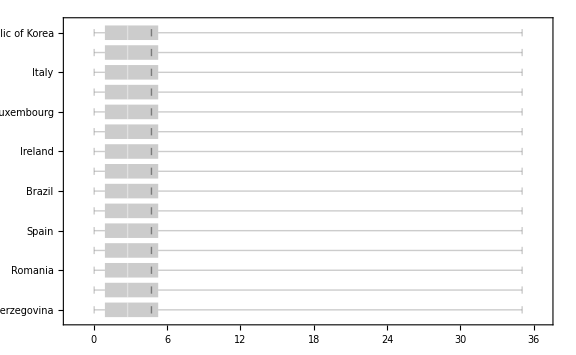
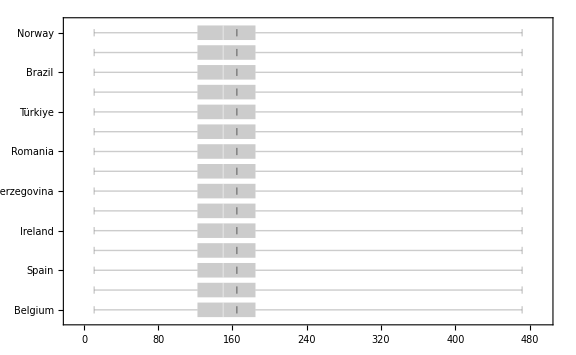
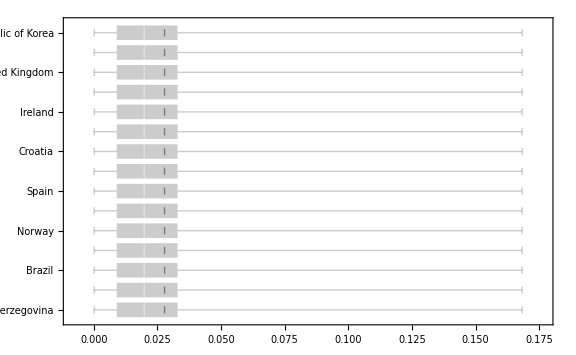

```mathematica
allBoxPlot=BoxWhiskerChart[
Table[Flatten@GatherBy[data[[2;;]],First][[All,All,#[[1]]]],Length[data2[[All,1,1]]]],
"Mean",
BarOrigin->Left,
ChartLabels->#[[3]],
ImageSize->Large,
ChartStyle->Opacity[0.4,Gray],
FrameTicksStyle->Directive[Black,12]]&/@{
{3,"Maximum number of cases/totalPop*100 by wave",Reverse@countriesOrderedByMaximum[[All,1]]},
{4,"Total number of cases/totalPop*100 by wave",Reverse@countriesOrderedByTotal[[All,1]]},
{5,"Wave span in days",Reverse@countriesOrderedByDuration[[All,1]]},
{6,"Ratio sum/span by waves",Reverse@countriesOrderedByRatio[[All,1]]}}
```

### Plot 5 - Merging

Plotting the Total number of cases/totalPop*100”|”Maximum number of cases/totalPop*100”|”Maximum number of cases/totalPop*100 normalized”  values of for all the waves of all countries in a unique BoxWhiskerChart and repeating this plot as many countries there are, and adding the points of the values belonging to each country

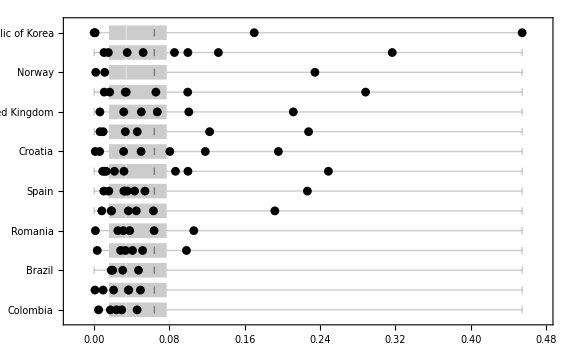
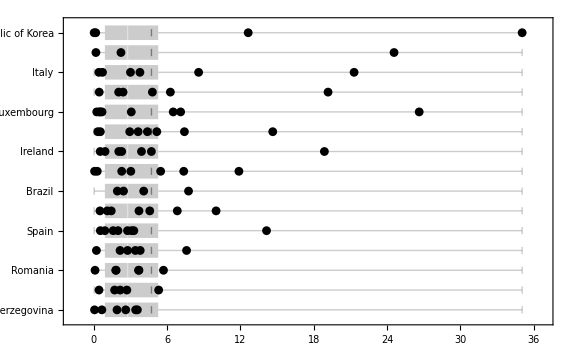
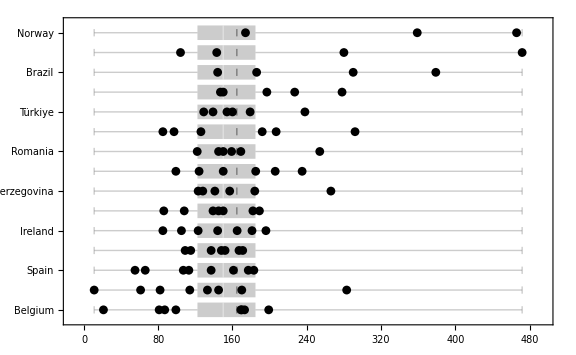
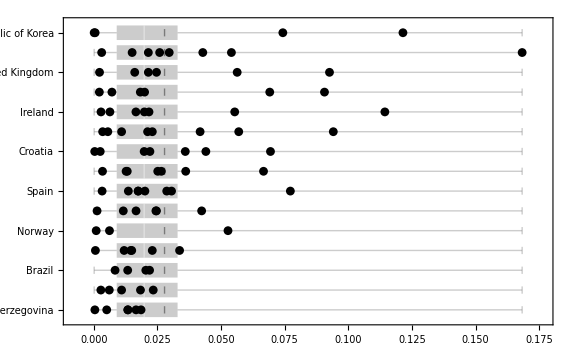

```mathematica
Show[allBoxPlot[[#]],listPlot2[[#]]]&/@{1,2,3,4}
```

### Ordered by the maximum value

### Plot 1

Merging the ListPlot and BoxWhiskerChart

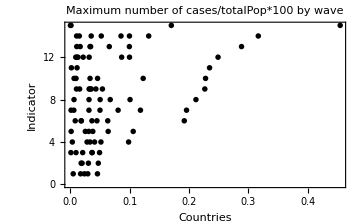
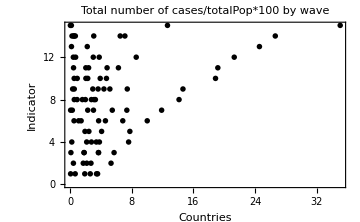
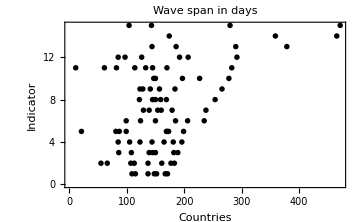
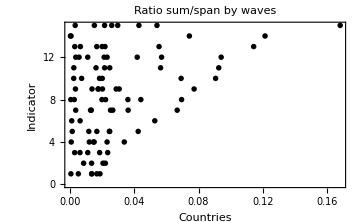

```mathematica
listPlot2=ListPlot[
(*Echo@*)Table[{#,i}&/@(#[[2]]/.#[[1]])[[i]],{i,1,15}],
PlotLabel->#[[3]],
PlotRange->All,
ImageSize->Medium,
Frame->True,
FrameLabel->{"Countries","Indicator"},
PlotStyle->Black
]&/@{
{Thread[data2[[All,All,1]][[All,1]]->data2[[All,All,3,2]]],Reverse@countriesOrderedByMaximum[[All,1]],"Maximum number of cases/totalPop*100 by wave"},
{Thread[data2[[All,All,1]][[All,1]]->data2[[All,All,4,2]]],Reverse@countriesOrderedByTotal[[All,1]],"Total number of cases/totalPop*100 by wave"},
{Thread[data2[[All,All,1]][[All,1]]->data2[[All,All,5,2]]],Reverse@countriesOrderedByDuration[[All,1]],
"Wave span in days"},
{Thread[data2[[All,All,1]][[All,1]]->data2[[All,All,6,2]]],Reverse@countriesOrderedByRatio[[All,1]],
"Ratio sum/span by waves"}
}
(*This listPlot2 is the same as listPlot2 but without Legends*)
```

### Plot 2

For all the waves of each country  is made a BoxWhiskerChart of the “Total number of cases/totalPop*100”,  “Maximum number of cases/totalPop*100”, “Maximum number of cases/totalPop*100 normalized”

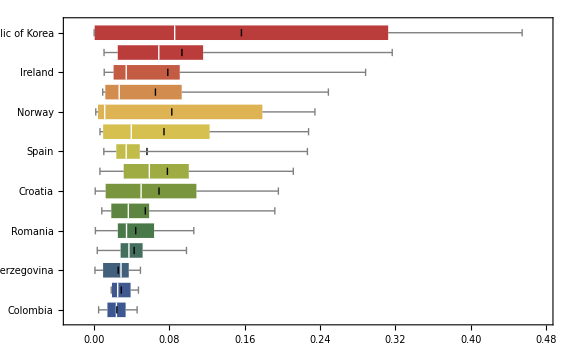
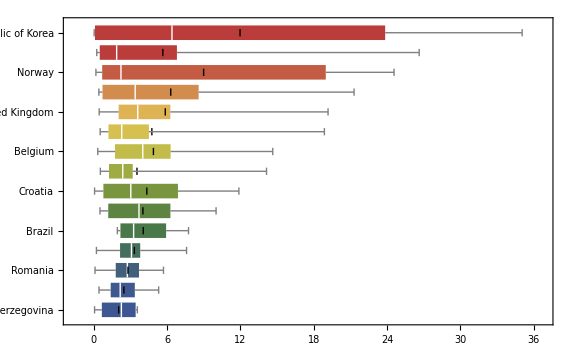
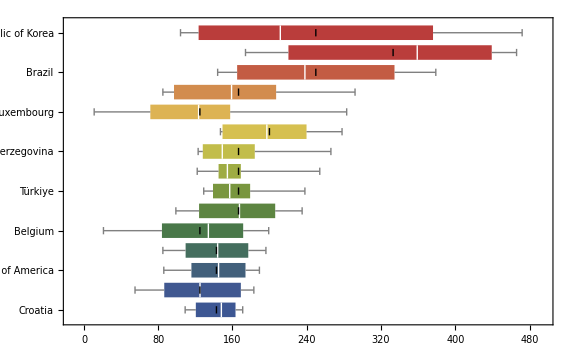
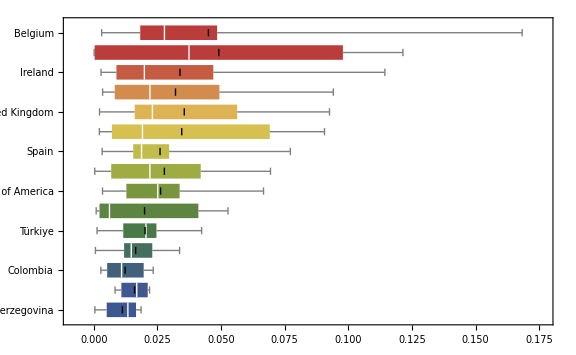

```mathematica
data3v2=GroupBy[data,First];
boxPlot=BoxWhiskerChart[
#[[2]]/.Normal[#[[1]]],
"Mean",
BarOrigin->Left,
ChartLabels->#[[2]],
ChartStyle->"DarkRainbow",
ImageSize->Large,
FrameTicksStyle->Directive[Black,12]
]&/@{
{data3[[2;;,All,3]],Reverse@countriesOrderedByMaximum[[All,1]],"Maximum number of cases/totalPop*100 by wave"},
{data3[[2;;,All,4]],Reverse@countriesOrderedByTotal[[All,1]],"Total number of cases/totalPop*100 by wave"},
{data3[[2;;,All,5]],Reverse@countriesOrderedByDuration[[All,1]],"Wave span in days"},
{data3[[2;;,All,6]],Reverse@countriesOrderedByRatio[[All,1]],"Ratio sum/span by waves"}}
```

### Plot 3

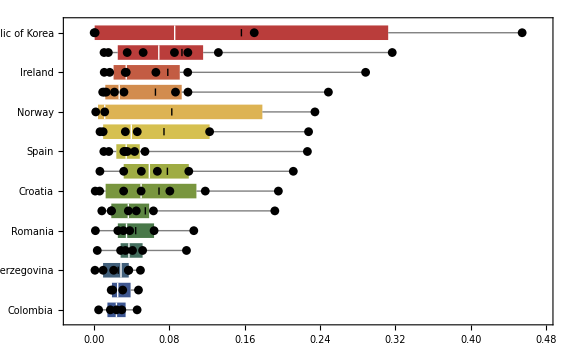
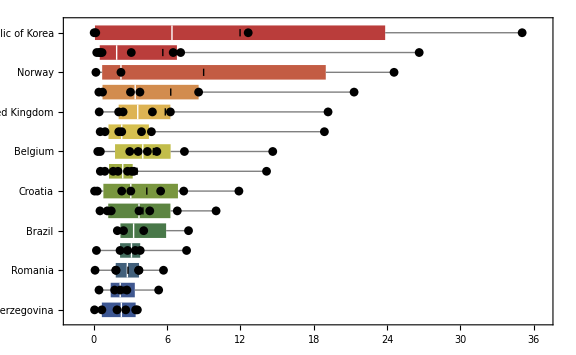
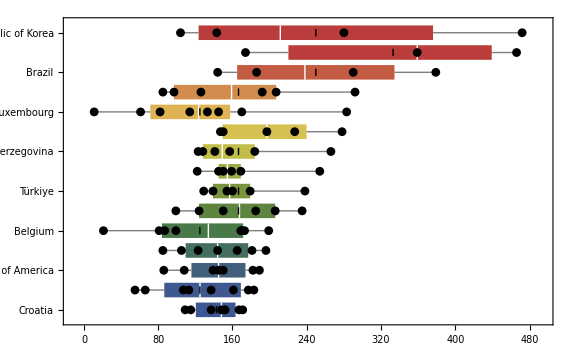
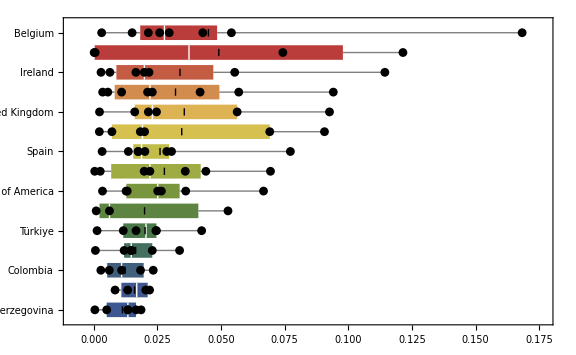

```mathematica
Show[boxPlot[[#]],listPlot2[[#]]]&/@{1,2,3,4}
```